```mathematica
Needs["PlotLegends`"]
```

```mathematica
v="9";
p="0.1";
ngap="4";
nvel="3";
jj=StringToStream[ngap];
ng= Read[jj,Number];
ii=StringToStream[nvel];
nv= Read[ii,Number];
g10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
g20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
g30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
g40k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l40k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
g50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l50k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];

gap10v9=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g10k1]}];
gap20v9=Table[{g20k1[[All,1]][[j]],Sum[g20k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g20k1]}];
gap30v9=Table[{g30k1[[All,1]][[j]],Sum[g30k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g30k1]}];
gap40v9=Table[{g40k1[[All,1]][[j]],Sum[g40k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g40k1]}];
gap50v9=Table[{g50k1[[All,1]][[j]],Sum[g50k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g50k1]}];
ga10k1=gap10v9[[All,1]];
ga20k1=gap20v9[[All,1]];
ga30k1=gap30v9[[All,1]];
ga40k1=gap40v9[[All,1]];
ga50k1=gap50v9[[All,1]];
ga10k2=gap10v9[[All,2]];
ga20k2=gap20v9[[All,2]];
ga30k2=gap30v9[[All,2]];
ga40k2=gap40v9[[All,2]];
ga50k2=gap50v9[[All,2]];
```

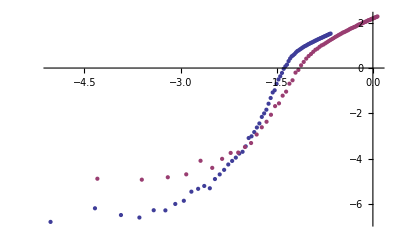

-4.29816

-0.659398

3.47952

```mathematica
v="9";
p="0.1";
ngap="3";
nvel="3";
jj=StringToStream[ngap];
ng= Read[jj,Number];
ii=StringToStream[nvel];
nv= Read[ii,Number];
ClearAll[d0,z,α];
d0=0.08;
z=0.454;
α=0.454;

g10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
g50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l50k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
gap10v9=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g10k1]}];
gap50v9=Table[{g50k1[[All,1]][[j]],Sum[g50k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g50k1]}];
ga10k1=gap10v9[[All,1]];
ga50k1=gap50v9[[All,1]];
ga10k2=gap10v9[[All,2]];
ga50k2=gap50v9[[All,2]];


j=1;
While[ga10k1[[j]]<d0,j++];
g10k=Table[{Log[ga10k1[[i]]-d0]+z*Log[10*1000.],
Log[ga10k2[[i]]]+α*Log[10*1000.]},{i,j+1,Length[ga10k1]}];
g50k=Table[{Log[ga50k1[[i]]-d0]+z*Log[50*1000.],Log[ga50k2[[i]]]+α*Log[50*1000.]},{i,j+1,Length[ga50k1]}];
ListPlot[{g10k,g50k}]
i10=Interpolation[g10k];
i50=Interpolation[g50k];
min=Max[Log[ga10k1[[j+1]]-d0]+z*Log[10*1000.],Log[ga50k1[[j+1]]-d0]+z*Log[50*1000.]]
max=Min[Log[ga10k1[[Length[ga10k1]]]-d0]+z*Log[10*1000.],Log[ga50k1[[Length[ga10k1]]]-d0]+z*Log[50*1000.]]
delta=(max-min)/50;
int=Sum[delta*(Max[i10[min+k*delta],i50[min+k*delta]]-Min[i10[min+k*delta],i50[min+k*delta]]),{k,0,50}]
```

0.283981  = val

0.0782  = d0

0.17  = α

0.17  = z

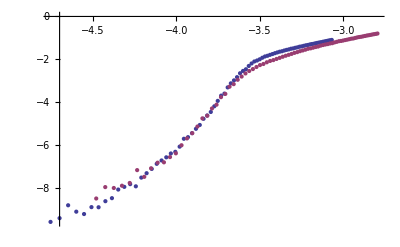

```mathematica
val=1000;
For[d0=0.064,d0<0.069,d0+=0.0005,
For[α=0.05,α<=1,α+=0.01,
z=α;
j=1;
While[ga10k1[[j]]<=d0,j++];
g10k=Table[{Log[ga10k1[[i]]-d0]+z*Log[10*1000.],
Log[ga10k2[[i]]]+α*Log[10*1000.]},{i,j,Length[ga10k1]}];
g50k=Table[{Log[ga50k1[[i]]-d0]+z*Log[50*1000.],Log[ga50k2[[i]]]+α*Log[50*1000.]},{i,j,Length[ga50k1]}];
i10=Interpolation[g10k];
i50=Interpolation[g50k];
min=Max[Log[ga10k1[[j]]-d0]+z*Log[10*1000.],Log[ga50k1[[j]]-d0]+z*Log[50*1000.]];
max=Min[Log[ga10k1[[Length[ga10k1]]]-d0]+z*Log[10*1000.],Log[ga50k1[[Length[ga50k1]]]-d0]+z*Log[50*1000.]];
delta=(max-min)/50;
int=Sum[delta*(Max[i10[min+k*delta],i50[min+k*delta]]-Min[i10[min+k*delta],i50[min+k*delta]]),{k,0,50}];
If[int<val,
val=int;
d0f=d0;
αf=α;
zf=z;]

]
]

" = val"  val
" = d0" d0f
" = α" αf
" = z" zf
g10k=Table[{Log[ga10k1[[i]]-d0f]+zf*Log[10*1000.],
Log[ga10k2[[i]]]+αf*Log[10*1000.]},{i,1,Length[ga10k1]}];
g50k=Table[{Log[ga50k1[[i]]-d0f]+zf*Log[50*1000.],Log[ga50k2[[i]]]+αf*Log[50*1000.]},{i,1,Length[ga50k1]}];
ListPlot[{g10k,g50k}]
```

```mathematica
v="7";
p="0.1";
ngap="3";
nvel="3";
jj=StringToStream[ngap];
ng= Read[jj,Number];
ii=StringToStream[nvel];
nv= Read[ii,Number];
g10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number}];
g50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number}];
gap10v9=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g10k1]}];
gap50v9=Table[{g50k1[[All,1]][[j]],Sum[g50k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g50k1]}];
ga10k1=gap10v9[[All,1]];
ga50k1=gap50v9[[All,1]];
ga10k2=gap10v9[[All,2]];
ga50k2=gap50v9[[All,2]];
```

```mathematica
ga10k1=gap10v10[[All,1]];
ga50k1=gap50v10[[All,1]];
ga10k2=gap10v10[[All,2]];
ga50k2=gap50v10[[All,2]];
```

0.275523  = val

0.0782  = d0

0.17  = α

0.17  = z

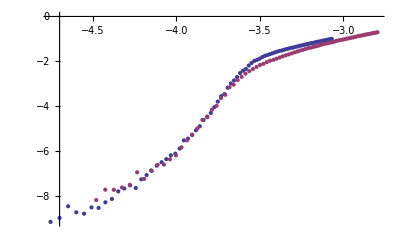

```mathematica
val=1000;
For[d0=0.0782,d0<=0.081,d0+=0.0001,
For[α=0.01,α<=1,α+=0.01,
z=α;
j=1;
While[ga10k1[[j]]<=d0,j++];
k=1;
While[ga50k1[[k]]<=d0,k++];
g10k=Table[{Log[ga10k1[[i]]-d0]+z*Log[10*1000.],
Log[ga10k2[[i]]]+α*Log[10*1000.]},{i,j,Length[ga10k1]-1}];
g50k=Table[{Log[ga50k1[[i]]-d0]+z*Log[50*1000.],Log[ga50k2[[i]]]+α*Log[50*1000.]},{i,k,Length[ga50k1]-1}];
i10=Interpolation[g10k];
i50=Interpolation[g50k];
min=Max[Log[ga10k1[[j]]-d0]+z*Log[10*1000.],Log[ga50k1[[k]]-d0]+z*Log[50*1000.]];
max=Min[Log[ga10k1[[Length[ga10k1]-1]]-d0]+z*Log[10*1000.],Log[ga50k1[[Length[ga10k1]-1]]-d0]+z*Log[50*1000.]];
delta=(max-min)/50;
int=Sum[delta*(Max[i10[min+k*delta],i50[min+k*delta]]-Min[i10[min+k*delta],i50[min+k*delta]]),{k,0,50}];
If[int<val,
val=int;
d0f=d0;
αf=α;
zf=z;]

]
]

" = val"  val
" = d0" d0f
" = α" αf
" = z" zf
g10k=Table[{Log[ga10k1[[i]]-d0f]+zf*Log[10*1000.],
Log[ga10k2[[i]]]+αf*Log[10*1000.]},{i,1,Length[ga10k1]}];
g50k=Table[{Log[ga50k1[[i]]-d0f]+zf*Log[50*1000.],Log[ga50k2[[i]]]+αf*Log[50*1000.]},{i,1,Length[ga50k1]}];
ListPlot[{g10k,g50k}]
```

```mathematica
ga10k1
```

{0.07,0.0701,0.0702,0.0703,0.0704,0.0705,0.0706,0.0707,0.0708,0.0709,0.071,0.0711,0.0712,0.0713,0.0714,0.0715,0.0716,0.0717,0.0718,0.0719,0.072,0.0721,0.0722,0.0723,0.0724,0.0725,0.0726,0.0727,0.0728,0.0729,0.073,0.0731,0.0732,0.0733,0.0734,0.0735,0.0736,0.0737,0.0738,0.0739,0.074,0.0741,0.0742,0.0743,0.0744,0.0745,0.0746,0.0747,0.0748,0.0749,0.075,0.0751,0.0752,0.0753,0.0754,0.0755,0.0756,0.0757,0.0758,0.0759,0.076,0.0761,0.0762,0.0763,0.0764,0.0765,0.0766,0.0767,0.0768,0.0769,0.077,0.0771,0.0772,0.0773,0.0774,0.0775,0.0776,0.0777,0.0778,0.0779,0.078,0.0781,0.0782,0.0783,0.0784,0.0785,0.0786,0.0787,0.0788,0.0789,0.079,0.0791,0.0792,0.0793,0.0794,0.0795,0.0796,0.0797,0.0798,0.0799}